## Definitions

```mathematica
fapprox[x_,L_, $N_]:=Sum[Cn[n]Exp[2ⅈ*n*π*x/L],{n,-$N,$N}];
fapprox[x_, L_, $N_, Coeffs_]:=Sum[Cn[n]Exp[2ⅈ*n*π*x/L],{n,Coeffs[[1;;$N]]}];
```

```mathematica
pointsraw = "366.1608769989015,61.74305137634278
366.4345677292348,62.69531416535378
366.71188702449206,63.66020196124911
366.9871484375,64.6179296875
367.2668360805511,65.59105776786805
367.70166503906256,65.56147949218749
367.97617837056515,64.60635459497571
368.25164489746095,63.64791320800782
368.5314617824555,62.6743354511261
368.80562874436384,61.72362472772599
369.13356099249796,60.769596705920996
369.4548920799978,59.83477293211968
369.779265504647,58.89109832126647
370.10786243686454,57.93513658527285
370.43367369771005,56.98727898836136
370.75828157642854,56.042922298349445
371.0815594169101,55.102434986098665
371.4062201349996,54.15792457457632
371.72868778675564,53.2197942819586
372.0545757433982,52.27171355987433
372.38195895388725,51.31928281098604
372.7090964794159,50.36756681442261
373.03442081717077,49.42112578534056
373.35652751263933,48.48404559503775
373.6838599869446,47.53176244901959
374.0058465731144,46.59503168344498
374.3313525095373,45.64806234335061
374.6596864952706,44.692865577302875
374.98011823942886,43.76065819378942
375.30696472481446,42.80978889788909
375.634573154666,41.85670293566305
375.9572440236737,40.917981438753195
376.2844088846238,39.96618591735431
376.61036479368806,39.01790750652552
376.93445139899586,38.075067317082436
377.25600834867686,37.13958645984065
377.58411352103434,36.1850553629169
377.9081061553955,35.2424885559082
378.23198628006503,34.300249064676464
378.5593917150866,33.347753659668385
378.88441725238664,32.40218190772633
379.21028661097165,31.454155291537752
379.5310683466308,30.52092970471829
379.8577102349489,29.570655627301896
380.18324276458617,28.62360892161785
380.50849186971783,27.677386761009693
380.8329968942492,26.73332929675933
381.16108013903715,25.778861992023884
381.48374272674556,24.840164587260226
381.8100507725775,23.890861732065677
382.13514843741433,22.945080145038666
382.45915916487576,22.002460701167585
383.2350236129761,21.68
384.2241793823242,21.68
385.2325016719103,21.68
386.2301931434125,21.68
387.2199246388674,21.68
388.2386157226563,21.68
389.2190831375122,21.68
390.234616394043,21.68
390.07068673355735,22.48562258287333
389.72214856779203,23.42373742379248
389.3740429551713,24.36068801768124
389.02395261911676,25.302980633452535
388.6810105419159,26.226033210754395
388.32922293428885,27.172894151626387
387.9804511384666,28.11163782417774
387.63630298053846,29.037936652079225
387.28556236878734,29.981979530351236
386.93632818928484,30.921967740905238
386.5855731563666,31.86604943475686
386.24128837527707,32.79271599344909
385.8933666609324,33.729171612270875
385.5429313422859,34.672392772807505
385.19749437953084,35.60216050900635
384.845228338888,36.550309185789665
384.5000632883262,37.47934505130979
384.1495571628041,38.42275679350249
383.8010729796998,39.360726336315274
383.45533107553376,40.291314843641594
383.10597422242165,41.23163323879242
382.7605140104136,42.16146355198114
382.40883987852754,43.10801906496272
382.0620519795871,44.041422940354096
381.7098641227372,44.98936117999256
381.3634759371914,45.92168919883669
381.0160994488187,46.85667730383575
380.66811722645537,47.7932957842201
380.3199118389376,48.73051492922008
379.9718658551015,49.66730502806604
379.62436184378345,50.60263636998832
379.2777823738195,51.53547924421728
378.9253334796036,52.48412008417654
378.57465370680904,53.42799921014346
378.2296938438772,54.35648279881207
377.8802294494211,55.29709064900875
377.53033433214057,56.2388578198012
377.1839849781803,57.17108132071793
376.8348099212544,58.11091039872379
376.4902326331404,59.03836426052265
376.13750684997854,59.98775036643841
375.7907570963166,60.921051571145654
375.44414412667277,61.853984612105414
375.0923933540494,62.80074640898965
374.74908256358697,63.724791403813285
374.39717935946334,64.67196348073776
374.0503440341368,65.60549500756315
373.69895339056853,66.5512874919176
373.3562732593715,67.47363502323628
373.0089635950886,68.40844326652586
372.65658419091517,69.35689706917736
372.3093153063697,70.29159555095248
371.96089347854024,71.22939726018348
371.6110848894157,72.17093153439463
371.26504838824275,73.10231297016144
370.91648687463487,74.04049065343105
370.56809770703313,74.97820445537567
369.57917609855537,75
368.58442635223264,75
367.57378867030144,75
366.5872482149303,75
365.5781888206303,75
364.5759523773193,75
364.09749848356466,74.26654311679303
363.7444074469991,73.31617390580476
363.40111228326333,72.39217097140848
363.05102131819615,71.44987666260567
362.7023403982699,70.51137758888187
362.35229497118155,69.56920584873296
362.0050370779258,68.63453695078265
361.6570411412418,67.6978815573454
361.3072694880167,66.75644669868983
360.9645395939052,65.83396522700787
360.6147710615283,64.89253876833362
360.26535519480706,63.95206153392792
359.9180782559016,63.017341373279926
359.56823262018065,62.075707385564456
359.2168695078791,61.12998900353908
358.8715443208444,60.200522119506495
358.52012649885614,59.25465648253448
358.17669772672264,58.330293931794586
357.8285632146895,57.3932655531168
357.47618183987885,56.4448064463574
357.12702968973696,55.50503902356257
356.78174491517944,54.5756809125375
356.4337856941539,53.63912434186204
356.0835590076447,52.69646472930908
355.7386732017994,51.76818047046662
355.38877143815847,50.82639541053053
355.0378321949803,49.88181790188537
354.68987662292,48.9452711526549
354.34167397515296,48.00805938188569
353.9936068205154,47.0712123003474
353.6460577278436,46.13575961880968
353.29940926597374,45.20273104804219
352.95404400374184,44.27315629881457
352.60320455744164,43.32884740044363
352.25450799060957,42.390306211978896
351.9083612842299,41.45862815119326
351.5582011860027,40.51614776565693
351.2115522582829,39.58311794102192
350.8620359986063,38.64237049195799
350.5103663922529,37.69582715976401
350.16392561410066,36.76335758424247
349.81670687183737,35.82879406392574
349.469576089296,34.894467293350026
349.1172457071743,33.94614543697797
348.773311913989,33.02042358676903
348.42659459397197,32.08720967948437
348.0731054246871,31.135768866447037
347.7263432850686,30.202434324071508
347.3772518539615,29.262830330803986
347.02889588162304,28.325205876231195
346.68001701354984,27.386174011230466
346.33543920366094,26.458718745037913
345.9846863460541,25.514642906188964
345.63913986360654,24.58458039008081
345.2885424245894,23.640922871232032
344.9380417716503,22.69752585887909
344.5921357822418,21.76649570465088
345.4582005596161,21.68
346.47543348506093,21.68
347.4756029987335,21.68
348.47499999999997,21.68
349.4743970012665,21.68
350.47456651493906,21.68
351.4610482895374,21.68
352.4123376941681,21.744985332489012
352.7372708487324,22.69028832245618
353.0634772266261,23.63929540295154
353.39139631701636,24.593285145945845
353.7165752591356,25.53930318670813
354.0373063259386,26.47238136652857
354.36290526747706,27.419621279239653
354.6909109768763,28.373863016242975
355.0165048199493,29.32108809638128
355.34401047095656,30.273875052034857
355.6663944044025,31.211761789423765
355.989919171799,32.15296746712178
356.317501290571,33.105976884551346
356.64321006913434,34.05353633765597
356.96564509263493,34.99157170740422
357.2932614202588,35.944680646010674
357.6154809792898,36.88208918157965
357.94117799154714,37.82961440387647
358.2646667635048,38.77071536281786
358.59019754663115,39.71775698751212
358.91710998905563,40.66881816714361
359.2447437389078,41.621977790896786
359.56739983430833,42.56065630808938
359.8894846835616,43.49767294288147
360.2153688526238,44.44574264605006
360.53935324015094,45.38828546117991
360.8656990215205,46.33769809746649
361.1935789685042,47.291573963564005
361.51730320123954,48.23335993040353
361.84086677059537,49.17467849165202
362.1678998837829,50.12609072943684
362.49249963629615,51.07042377850565
362.8178806627193,52.01702972756233
363.14237189109645,52.961047055724194
363.46822088828105,53.909014436059515
363.79285261020067,54.8534404912591
364.1207799626538,55.80745427043643
364.4438618732989,56.74737157911062
364.7702626004326,57.69694406487513
365.09094933358955,58.62989326823503
365.4196649932862,59.58620040893555
365.74037258839235,60.51921030435712
366.06842705221845,61.47359387885779";
```

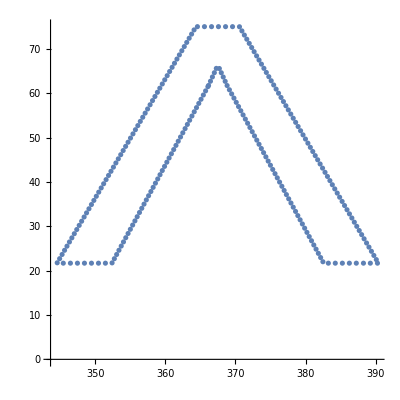

```mathematica
points = ToExpression[StringJoin["{{",StringReplace[pointsraw, "\n"->"},{"],"}}"]];
ListPlot[points, AspectRatio->1]
```

```mathematica
points = {#[[1]],-#[[2]]}&/@points
```

{{366.161,-61.7431},{366.435,-62.6953},{366.712,-63.6602},{366.987,-64.6179},{367.267,-65.5911},{367.702,-65.5615},{367.976,-64.6064},{368.252,-63.6479},{368.531,-62.6743},{368.806,-61.7236},{369.134,-60.7696},{369.455,-59.8348},{369.779,-58.8911},{370.108,-57.9351},{370.434,-56.9873},{370.758,-56.0429},{371.082,-55.1024},{371.406,-54.1579},{371.729,-53.2198},{372.055,-52.2717},{372.382,-51.3193},{372.709,-50.3676},{373.034,-49.4211},{373.357,-48.484},{373.684,-47.5318},{374.006,-46.595},{374.331,-45.6481},{374.66,-44.6929},{374.98,-43.7607},{375.307,-42.8098},{375.635,-41.8567},{375.957,-40.918},{376.284,-39.9662},{376.61,-39.0179},{376.934,-38.0751},{377.256,-37.1396},{377.584,-36.1851},{377.908,-35.2425},{378.232,-34.3002},{378.559,-33.3478},{378.884,-32.4022},{379.21,-31.4542},{379.531,-30.5209},{379.858,-29.5707},{380.183,-28.6236},{380.508,-27.6774},{380.833,-26.7333},{381.161,-25.7789},{381.484,-24.8402},{381.81,-23.8909},{382.135,-22.9451},{382.459,-22.0025},{383.235,-21.68},{384.224,-21.68},{385.233,-21.68},{386.23,-21.68},{387.22,-21.68},{388.239,-21.68},{389.219,-21.68},{390.235,-21.68},{390.071,-22.4856},{389.722,-23.4237},{389.374,-24.3607},{389.024,-25.303},{388.681,-26.226},{388.329,-27.1729},{387.98,-28.1116},{387.636,-29.0379},{387.286,-29.982},{386.936,-30.922},{386.586,-31.866},{386.241,-32.7927},{385.893,-33.7292},{385.543,-34.6724},{385.197,-35.6022},{384.845,-36.5503},{384.5,-37.4793},{384.15,-38.4228},{383.801,-39.3607},{383.455,-40.2913},{383.106,-41.2316},{382.761,-42.1615},{382.409,-43.108},{382.062,-44.0414},{381.71,-44.9894},{381.363,-45.9217},{381.016,-46.8567},{380.668,-47.7933},{380.32,-48.7305},{379.972,-49.6673},{379.624,-50.6026},{379.278,-51.5355},{378.925,-52.4841},{378.575,-53.428},{378.23,-54.3565},{377.88,-55.2971},{377.53,-56.2389},{377.184,-57.1711},{376.835,-58.1109},{376.49,-59.0384},{376.138,-59.9878},{375.791,-60.9211},{375.444,-61.854},{375.092,-62.8007},{374.749,-63.7248},{374.397,-64.672},{374.05,-65.6055},{373.699,-66.5513},{373.356,-67.4736},{373.009,-68.4084},{372.657,-69.3569},{372.309,-70.2916},{371.961,-71.2294},{371.611,-72.1709},{371.265,-73.1023},{370.916,-74.0405},{370.568,-74.9782},{369.579,-75},{368.584,-75},{367.574,-75},{366.587,-75},{365.578,-75},{364.576,-75},{364.097,-74.2665},{363.744,-73.3162},{363.401,-72.3922},{363.051,-71.4499},{362.702,-70.5114},{362.352,-69.5692},{362.005,-68.6345},{361.657,-67.6979},{361.307,-66.7564},{360.965,-65.834},{360.615,-64.8925},{360.265,-63.9521},{359.918,-63.0173},{359.568,-62.0757},{359.217,-61.13},{358.872,-60.2005},{358.52,-59.2547},{358.177,-58.3303},{357.829,-57.3933},{357.476,-56.4448},{357.127,-55.505},{356.782,-54.5757},{356.434,-53.6391},{356.084,-52.6965},{355.739,-51.7682},{355.389,-50.8264},{355.038,-49.8818},{354.69,-48.9453},{354.342,-48.0081},{353.994,-47.0712},{353.646,-46.1358},{353.299,-45.2027},{352.954,-44.2732},{352.603,-43.3288},{352.255,-42.3903},{351.908,-41.4586},{351.558,-40.5161},{351.212,-39.5831},{350.862,-38.6424},{350.51,-37.6958},{350.164,-36.7634},{349.817,-35.8288},{349.47,-34.8945},{349.117,-33.9461},{348.773,-33.0204},{348.427,-32.0872},{348.073,-31.1358},{347.726,-30.2024},{347.377,-29.2628},{347.029,-28.3252},{346.68,-27.3862},{346.335,-26.4587},{345.985,-25.5146},{345.639,-24.5846},{345.289,-23.6409},{344.938,-22.6975},{344.592,-21.7665},{345.458,-21.68},{346.475,-21.68},{347.476,-21.68},{348.475,-21.68},{349.474,-21.68},{350.475,-21.68},{351.461,-21.68},{352.412,-21.745},{352.737,-22.6903},{353.063,-23.6393},{353.391,-24.5933},{353.717,-25.5393},{354.037,-26.4724},{354.363,-27.4196},{354.691,-28.3739},{355.017,-29.3211},{355.344,-30.2739},{355.666,-31.2118},{355.99,-32.153},{356.318,-33.106},{356.643,-34.0535},{356.966,-34.9916},{357.293,-35.9447},{357.615,-36.8821},{357.941,-37.8296},{358.265,-38.7707},{358.59,-39.7178},{358.917,-40.6688},{359.245,-41.622},{359.567,-42.5607},{359.889,-43.4977},{360.215,-44.4457},{360.539,-45.3883},{360.866,-46.3377},{361.194,-47.2916},{361.517,-48.2334},{361.841,-49.1747},{362.168,-50.1261},{362.492,-51.0704},{362.818,-52.017},{363.142,-52.961},{363.468,-53.909},{363.793,-54.8534},{364.121,-55.8075},{364.444,-56.7474},{364.77,-57.6969},{365.091,-58.6299},{365.42,-59.5862},{365.74,-60.5192},{366.068,-61.4736}}

```mathematica
pointscentered =(#-Mean@points)&/@points
```

{{-1.30445,-16.2913},{-1.03076,-17.2436},{-0.753442,-18.2084},{-0.478181,-19.1662},{-0.198493,-20.1393},{0.236336,-20.1097},{0.510849,-19.1546},{0.786316,-18.1962},{1.06613,-17.2226},{1.3403,-16.2719},{1.66823,-15.3178},{1.98956,-14.383},{2.31394,-13.4393},{2.64253,-12.4834},{2.96834,-11.5355},{3.29295,-10.5912},{3.61623,-9.65068},{3.94089,-8.70617},{4.26336,-7.76804},{4.58925,-6.81995},{4.91663,-5.86752},{5.24377,-4.91581},{5.56909,-3.96937},{5.8912,-3.03229},{6.21853,-2.08},{6.54052,-1.14327},{6.86602,-0.196303},{7.19436,0.758894},{7.51479,1.6911},{7.84164,2.64197},{8.16924,3.59506},{8.49191,4.53378},{8.81908,5.48557},{9.14504,6.43385},{9.46912,7.37669},{9.79068,8.31217},{10.1188,9.2667},{10.4428,10.2093},{10.7667,11.1515},{11.0941,12.104},{11.4191,13.0496},{11.745,13.9976},{12.0657,14.9308},{12.3924,15.8811},{12.7179,16.8282},{13.0432,17.7744},{13.3677,18.7184},{13.6958,19.6729},{14.0184,20.6116},{14.3447,21.5609},{14.6698,22.5067},{14.9938,23.4493},{15.7697,23.7718},{16.7589,23.7718},{17.7672,23.7718},{18.7649,23.7718},{19.7546,23.7718},{20.7733,23.7718},{21.7538,23.7718},{22.7693,23.7718},{22.6054,22.9661},{22.2568,22.028},{21.9087,21.0911},{21.5586,20.1488},{21.2157,19.2257},{20.8639,18.2789},{20.5151,17.3401},{20.171,16.4138},{19.8202,15.4698},{19.471,14.5298},{19.1202,13.5857},{18.776,12.659},{18.428,11.7226},{18.0776,10.7794},{17.7322,9.8496},{17.3799,8.90145},{17.0347,7.97241},{16.6842,7.029},{16.3357,6.09103},{15.99,5.16044},{15.6406,4.22013},{15.2952,3.2903},{14.9435,2.34374},{14.5967,1.41034},{14.2445,0.462398},{13.8981,-0.46993},{13.5508,-1.40492},{13.2028,-2.34154},{12.8546,-3.27876},{12.5065,-4.21555},{12.159,-5.15088},{11.8125,-6.08372},{11.46,-7.03236},{11.1093,-7.97624},{10.7644,-8.90472},{10.4149,-9.84533},{10.065,-10.7871},{9.71866,-11.7193},{9.36948,-12.6592},{9.0249,-13.5866},{8.67218,-14.536},{8.32543,-15.4693},{7.97881,-16.4022},{7.62706,-17.349},{7.28375,-18.273},{6.93185,-19.2202},{6.58501,-20.1537},{6.23362,-21.0995},{5.89094,-22.0219},{5.54363,-22.9567},{5.19126,-23.9051},{4.84399,-24.8398},{4.49556,-25.7776},{4.14576,-26.7192},{3.79972,-27.6506},{3.45116,-28.5887},{3.10277,-29.5264},{2.11385,-29.5482},{1.1191,-29.5482},{0.108459,-29.5482},{-0.878081,-29.5482},{-1.88714,-29.5482},{-2.88938,-29.5482},{-3.36783,-28.8148},{-3.72092,-27.8644},{-4.06422,-26.9404},{-4.41431,-25.9981},{-4.76299,-25.0596},{-5.11303,-24.1174},{-5.46029,-23.1828},{-5.80829,-22.2461},{-6.15806,-21.3047},{-6.50079,-20.3822},{-6.85056,-19.4408},{-7.19997,-18.5003},{-7.54725,-17.5656},{-7.8971,-16.6239},{-8.24846,-15.6782},{-8.59378,-14.7488},{-8.9452,-13.8029},{-9.28863,-12.8785},{-9.63677,-11.9415},{-9.98915,-10.993},{-10.3383,-10.0533},{-10.6836,-9.12392},{-11.0315,-8.18737},{-11.3818,-7.24471},{-11.7267,-6.31642},{-12.0766,-5.37464},{-12.4275,-4.43006},{-12.7755,-3.49351},{-13.1237,-2.5563},{-13.4717,-1.61945},{-13.8193,-0.684},{-14.1659,0.249028},{-14.5113,1.1786},{-14.8621,2.12291},{-15.2108,3.06145},{-15.557,3.99313},{-15.9071,4.93561},{-16.2538,5.86864},{-16.6033,6.80939},{-16.955,7.75593},{-17.3014,8.6884},{-17.6486,9.62297},{-17.9958,10.5573},{-18.3481,11.5056},{-18.692,12.4313},{-19.0387,13.3645},{-19.3922,14.316},{-19.739,15.2493},{-20.0881,16.1889},{-20.4364,17.1266},{-20.7853,18.0656},{-21.1299,18.993},{-21.4806,19.9371},{-21.8262,20.8672},{-22.1768,21.8108},{-22.5273,22.7542},{-22.8732,23.6853},{-22.0071,23.7718},{-20.9899,23.7718},{-19.9897,23.7718},{-18.9903,23.7718},{-17.9909,23.7718},{-16.9908,23.7718},{-16.0043,23.7718},{-15.053,23.7068},{-14.7281,22.7615},{-14.4019,21.8125},{-14.0739,20.8585},{-13.7488,19.9125},{-13.428,18.9794},{-13.1024,18.0321},{-12.7744,17.0779},{-12.4488,16.1307},{-12.1213,15.1779},{-11.7989,14.24},{-11.4754,13.2988},{-11.1478,12.3458},{-10.8221,11.3982},{-10.4997,10.4602},{-10.1721,9.50708},{-9.84985,8.56967},{-9.52415,7.62214},{-9.20066,6.68104},{-8.87513,5.734},{-8.54822,4.78294},{-8.22059,3.82978},{-7.89793,2.8911},{-7.57584,1.95409},{-7.24996,1.00602},{-6.92598,0.0634737},{-6.59963,-0.885939},{-6.27175,-1.83981},{-5.94803,-2.7816},{-5.62446,-3.72292},{-5.29743,-4.67433},{-4.97283,-5.61866},{-4.64745,-6.56527},{-4.32296,-7.50929},{-3.99711,-8.45726},{-3.67248,-9.40168},{-3.34455,-10.3557},{-3.02147,-11.2956},{-2.69507,-12.2452},{-2.37438,-13.1781},{-2.04566,-14.1344},{-1.72496,-15.0675},{-1.3969,-16.0218}}

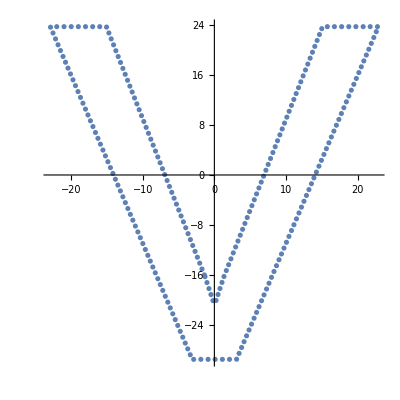

```mathematica
ListPlot[pointscentered, AspectRatio->1]
```

```mathematica
complexpoints =Complex@@@pointscentered
```

{-1.30445-16.2913 ⅈ,-1.03076-17.2436 ⅈ,-0.753442-18.2084 ⅈ,-0.478181-19.1662 ⅈ,-0.198493-20.1393 ⅈ,0.236336-20.1097 ⅈ,0.510849-19.1546 ⅈ,0.786316-18.1962 ⅈ,1.06613-17.2226 ⅈ,1.3403-16.2719 ⅈ,1.66823-15.3178 ⅈ,1.98956-14.383 ⅈ,2.31394-13.4393 ⅈ,2.64253-12.4834 ⅈ,2.96834-11.5355 ⅈ,3.29295-10.5912 ⅈ,3.61623-9.65068 ⅈ,3.94089-8.70617 ⅈ,4.26336-7.76804 ⅈ,4.58925-6.81995 ⅈ,4.91663-5.86752 ⅈ,5.24377-4.91581 ⅈ,5.56909-3.96937 ⅈ,5.8912-3.03229 ⅈ,6.21853-2.08 ⅈ,6.54052-1.14327 ⅈ,6.86602-0.196303 ⅈ,7.19436+0.758894 ⅈ,7.51479+1.6911 ⅈ,7.84164+2.64197 ⅈ,8.16924+3.59506 ⅈ,8.49191+4.53378 ⅈ,8.81908+5.48557 ⅈ,9.14504+6.43385 ⅈ,9.46912+7.37669 ⅈ,9.79068+8.31217 ⅈ,10.1188+9.2667 ⅈ,10.4428+10.2093 ⅈ,10.7667+11.1515 ⅈ,11.0941+12.104 ⅈ,11.4191+13.0496 ⅈ,11.745+13.9976 ⅈ,12.0657+14.9308 ⅈ,12.3924+15.8811 ⅈ,12.7179+16.8282 ⅈ,13.0432+17.7744 ⅈ,13.3677+18.7184 ⅈ,13.6958+19.6729 ⅈ,14.0184+20.6116 ⅈ,14.3447+21.5609 ⅈ,14.6698+22.5067 ⅈ,14.9938+23.4493 ⅈ,15.7697+23.7718 ⅈ,16.7589+23.7718 ⅈ,17.7672+23.7718 ⅈ,18.7649+23.7718 ⅈ,19.7546+23.7718 ⅈ,20.7733+23.7718 ⅈ,21.7538+23.7718 ⅈ,22.7693+23.7718 ⅈ,22.6054+22.9661 ⅈ,22.2568+22.028 ⅈ,21.9087+21.0911 ⅈ,21.5586+20.1488 ⅈ,21.2157+19.2257 ⅈ,20.8639+18.2789 ⅈ,20.5151+17.3401 ⅈ,20.171+16.4138 ⅈ,19.8202+15.4698 ⅈ,19.471+14.5298 ⅈ,19.1202+13.5857 ⅈ,18.776+12.659 ⅈ,18.428+11.7226 ⅈ,18.0776+10.7794 ⅈ,17.7322+9.8496 ⅈ,17.3799+8.90145 ⅈ,17.0347+7.97241 ⅈ,16.6842+7.029 ⅈ,16.3357+6.09103 ⅈ,15.99+5.16044 ⅈ,15.6406+4.22013 ⅈ,15.2952+3.2903 ⅈ,14.9435+2.34374 ⅈ,14.5967+1.41034 ⅈ,14.2445+0.462398 ⅈ,13.8981-0.46993 ⅈ,13.5508-1.40492 ⅈ,13.2028-2.34154 ⅈ,12.8546-3.27876 ⅈ,12.5065-4.21555 ⅈ,12.159-5.15088 ⅈ,11.8125-6.08372 ⅈ,11.46-7.03236 ⅈ,11.1093-7.97624 ⅈ,10.7644-8.90472 ⅈ,10.4149-9.84533 ⅈ,10.065-10.7871 ⅈ,9.71866-11.7193 ⅈ,9.36948-12.6592 ⅈ,9.0249-13.5866 ⅈ,8.67218-14.536 ⅈ,8.32543-15.4693 ⅈ,7.97881-16.4022 ⅈ,7.62706-17.349 ⅈ,7.28375-18.273 ⅈ,6.93185-19.2202 ⅈ,6.58501-20.1537 ⅈ,6.23362-21.0995 ⅈ,5.89094-22.0219 ⅈ,5.54363-22.9567 ⅈ,5.19126-23.9051 ⅈ,4.84399-24.8398 ⅈ,4.49556-25.7776 ⅈ,4.14576-26.7192 ⅈ,3.79972-27.6506 ⅈ,3.45116-28.5887 ⅈ,3.10277-29.5264 ⅈ,2.11385-29.5482 ⅈ,1.1191-29.5482 ⅈ,0.108459-29.5482 ⅈ,-0.878081-29.5482 ⅈ,-1.88714-29.5482 ⅈ,-2.88938-29.5482 ⅈ,-3.36783-28.8148 ⅈ,-3.72092-27.8644 ⅈ,-4.06422-26.9404 ⅈ,-4.41431-25.9981 ⅈ,-4.76299-25.0596 ⅈ,-5.11303-24.1174 ⅈ,-5.46029-23.1828 ⅈ,-5.80829-22.2461 ⅈ,-6.15806-21.3047 ⅈ,-6.50079-20.3822 ⅈ,-6.85056-19.4408 ⅈ,-7.19997-18.5003 ⅈ,-7.54725-17.5656 ⅈ,-7.8971-16.6239 ⅈ,-8.24846-15.6782 ⅈ,-8.59378-14.7488 ⅈ,-8.9452-13.8029 ⅈ,-9.28863-12.8785 ⅈ,-9.63677-11.9415 ⅈ,-9.98915-10.993 ⅈ,-10.3383-10.0533 ⅈ,-10.6836-9.12392 ⅈ,-11.0315-8.18737 ⅈ,-11.3818-7.24471 ⅈ,-11.7267-6.31642 ⅈ,-12.0766-5.37464 ⅈ,-12.4275-4.43006 ⅈ,-12.7755-3.49351 ⅈ,-13.1237-2.5563 ⅈ,-13.4717-1.61945 ⅈ,-13.8193-0.684 ⅈ,-14.1659+0.249028 ⅈ,-14.5113+1.1786 ⅈ,-14.8621+2.12291 ⅈ,-15.2108+3.06145 ⅈ,-15.557+3.99313 ⅈ,-15.9071+4.93561 ⅈ,-16.2538+5.86864 ⅈ,-16.6033+6.80939 ⅈ,-16.955+7.75593 ⅈ,-17.3014+8.6884 ⅈ,-17.6486+9.62297 ⅈ,-17.9958+10.5573 ⅈ,-18.3481+11.5056 ⅈ,-18.692+12.4313 ⅈ,-19.0387+13.3645 ⅈ,-19.3922+14.316 ⅈ,-19.739+15.2493 ⅈ,-20.0881+16.1889 ⅈ,-20.4364+17.1266 ⅈ,-20.7853+18.0656 ⅈ,-21.1299+18.993 ⅈ,-21.4806+19.9371 ⅈ,-21.8262+20.8672 ⅈ,-22.1768+21.8108 ⅈ,-22.5273+22.7542 ⅈ,-22.8732+23.6853 ⅈ,-22.0071+23.7718 ⅈ,-20.9899+23.7718 ⅈ,-19.9897+23.7718 ⅈ,-18.9903+23.7718 ⅈ,-17.9909+23.7718 ⅈ,-16.9908+23.7718 ⅈ,-16.0043+23.7718 ⅈ,-15.053+23.7068 ⅈ,-14.7281+22.7615 ⅈ,-14.4019+21.8125 ⅈ,-14.0739+20.8585 ⅈ,-13.7488+19.9125 ⅈ,-13.428+18.9794 ⅈ,-13.1024+18.0321 ⅈ,-12.7744+17.0779 ⅈ,-12.4488+16.1307 ⅈ,-12.1213+15.1779 ⅈ,-11.7989+14.24 ⅈ,-11.4754+13.2988 ⅈ,-11.1478+12.3458 ⅈ,-10.8221+11.3982 ⅈ,-10.4997+10.4602 ⅈ,-10.1721+9.50708 ⅈ,-9.84985+8.56967 ⅈ,-9.52415+7.62214 ⅈ,-9.20066+6.68104 ⅈ,-8.87513+5.734 ⅈ,-8.54822+4.78294 ⅈ,-8.22059+3.82978 ⅈ,-7.89793+2.8911 ⅈ,-7.57584+1.95409 ⅈ,-7.24996+1.00602 ⅈ,-6.92598+0.0634737 ⅈ,-6.59963-0.885939 ⅈ,-6.27175-1.83981 ⅈ,-5.94803-2.7816 ⅈ,-5.62446-3.72292 ⅈ,-5.29743-4.67433 ⅈ,-4.97283-5.61866 ⅈ,-4.64745-6.56527 ⅈ,-4.32296-7.50929 ⅈ,-3.99711-8.45726 ⅈ,-3.67248-9.40168 ⅈ,-3.34455-10.3557 ⅈ,-3.02147-11.2956 ⅈ,-2.69507-12.2452 ⅈ,-2.37438-13.1781 ⅈ,-2.04566-14.1344 ⅈ,-1.72496-15.0675 ⅈ,-1.3969-16.0218 ⅈ}

```mathematica
Linear
```

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@complexpoints,AspectRatio->1]
```

-Graphics-

```mathematica
Manipulate[ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@complexpoints[[1;;n]],AspectRatio->1], {n,1,Length@polarpoints,1}]
```

```mathematica
Cn[n_]:=fcomplexpoints[[n+1]]
```

```mathematica
Cn[n_]:=1/Length[complexpoints] Sum[complexpoints[[x]]*Exp[-2 Pi ⅈ n x/Length[complexpoints]],{x,1,Length[complexpoints]}]
```

```mathematica
Cn[-1]
```

-1.71769+12.2322 ⅈ

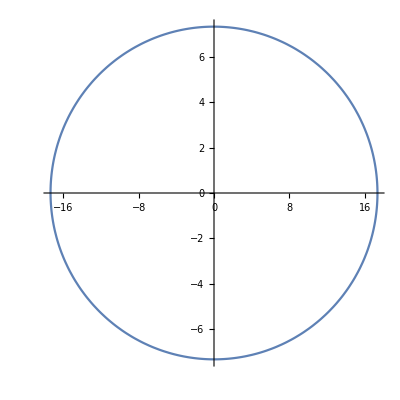
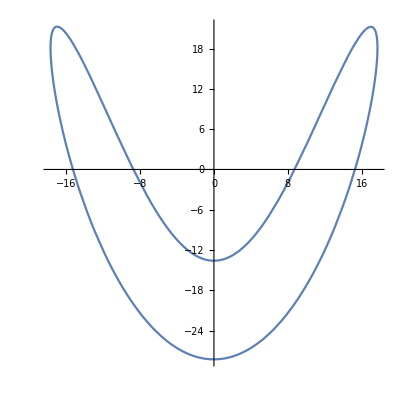
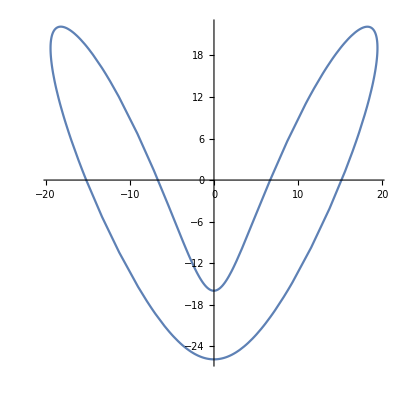
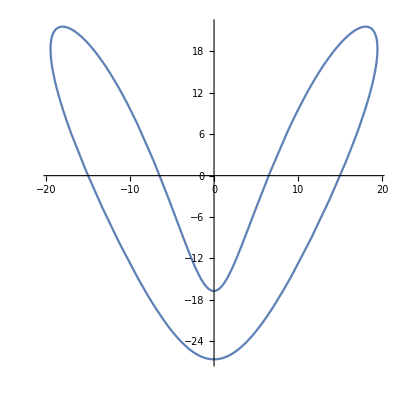
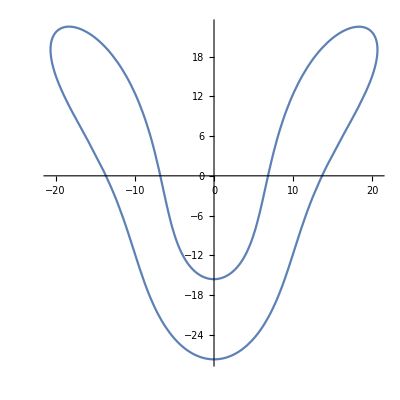
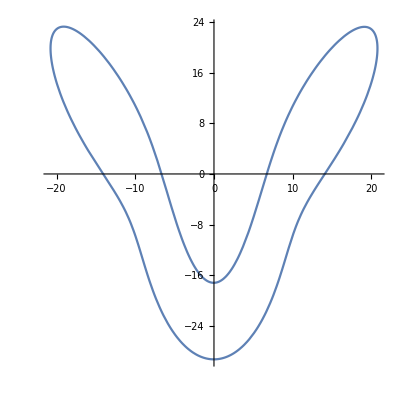
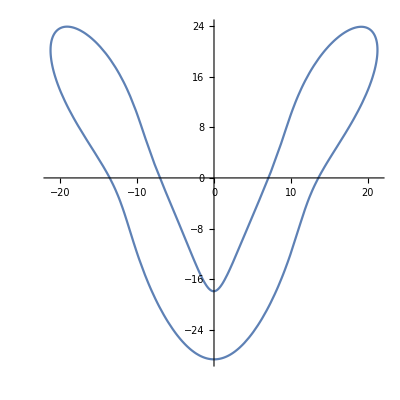
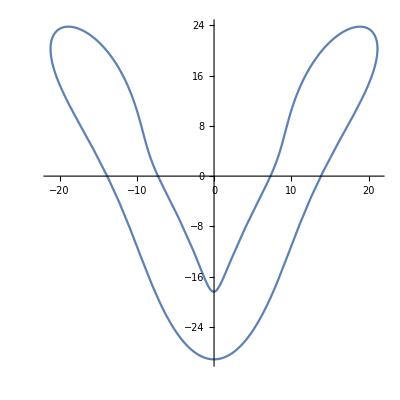
{3
-Graphics-,5
-Graphics-,7
-Graphics-,9
-Graphics-,11
-Graphics-,13
-Graphics-,15
-Graphics-,17
-Graphics-,19
-Graphics-,21
-Graphics-}

```mathematica
Table[With[{approx = fapprox[x, Length[fcomplexpoints], n]},Column[{Length@approx,ParametricPlot[{Re@approx, Im@approx},{x,0,Length[fpolarpoints]}, AspectRatio->1]}]],{n,1,10}]
```

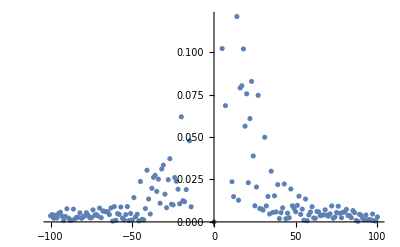

```mathematica
coefficients = Table[{n,Abs[Cn[n]]},{n,-100,100}];
ListPlot[coefficients]
```

```mathematica
SortedCoeffs = First/@Reverse@SortBy[coefficients, Last]
```

{-1,-2,2,1,-3,-5,-6,6,-7,-9,4,-8,-4,-12,3,-11,9,10,13,-16,8,-10,-13,14,5,18,23,17,16,20,27,7,-20,22,19,31,-15,24,-27,-31,-32,-41,35,-36,-37,-24,-34,-28,-23,-45,11,21,43,39,26,-38,47,-22,-17,-35,-30,37,52,33,12,-49,-40,56,15,-19,-18,-33,-21,-26,-25,51,48,25,32,72,76,-61,-53,60,-14,-57,-29,42,-63,-70,49,-42,28,-90,29,54,-86,81,68,-74,30,85,-68,-67,63,-65,50,-66,38,59,64,80,79,-94,36,75,86,-78,41,-82,45,77,-95,-51,-59,71,34,-39,97,-47,89,53,-58,-72,-64,-99,-54,67,93,58,66,69,-97,-77,90,-73,82,83,65,-79,-100,-71,70,-93,-91,-80,100,-48,74,-83,-84,-69,84,46,-76,-75,78,-96,61,-89,-56,-98,73,62,-81,40,91,44,-85,-44,95,92,-55,94,96,-43,-50,-87,55,-60,-88,-92,87,-52,57,98,99,-46,-62,88,0}

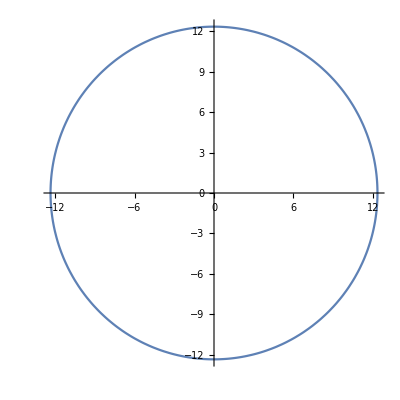
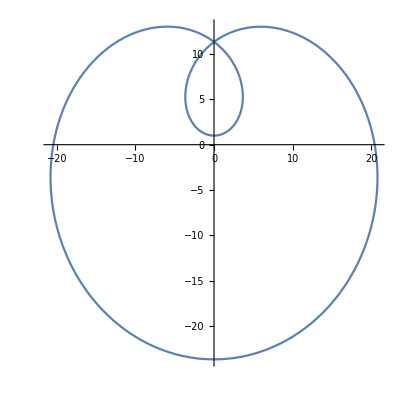
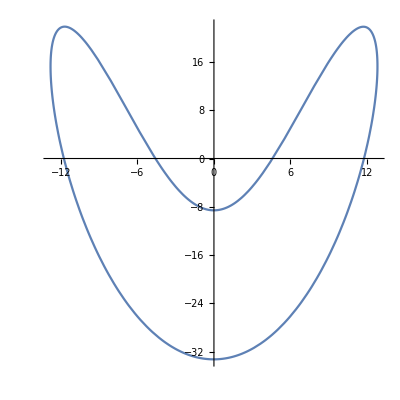
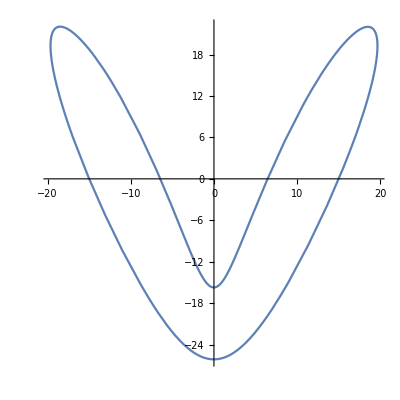
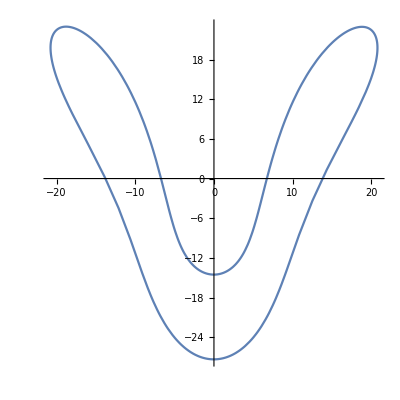
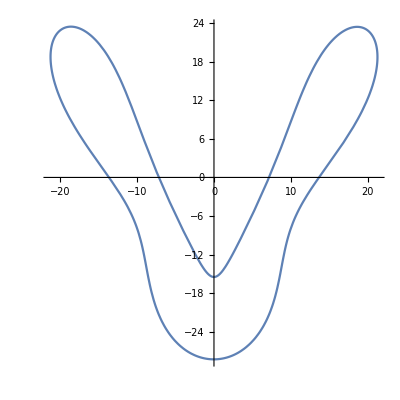
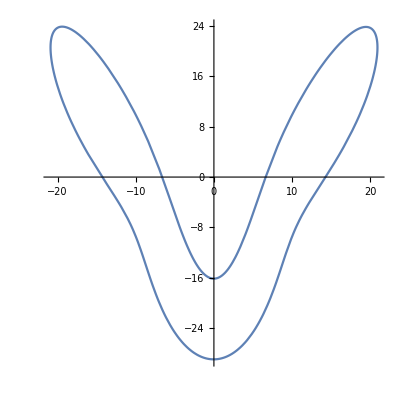
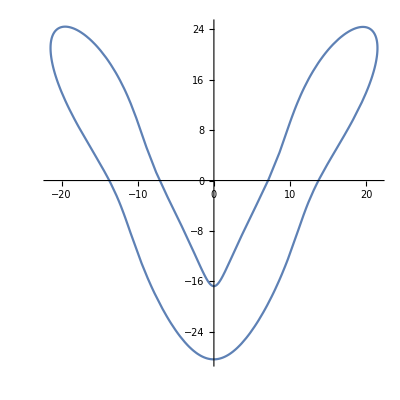
{2
-Graphics-,2
-Graphics-,3
-Graphics-,4
-Graphics-,5
-Graphics-,6
-Graphics-,7
-Graphics-,8
-Graphics-,9
-Graphics-,10
-Graphics-,11
-Graphics-,12
-Graphics-,13
-Graphics-,14
-Graphics-,15
-Graphics-,16
-Graphics-,17
-Graphics-,18
-Graphics-,19
-Graphics-,20
-Graphics-,21
-Graphics-}

```mathematica
Table[With[{approx = fapprox[x, Length[fcomplexpoints], n, SortedCoeffs]},Column[{Length@approx,ParametricPlot[{Re@approx, Im@approx},{x,0,Length[fpolarpoints]}, AspectRatio->1]}]],{n,1,21}]
```

```mathematica
fapprox[x, Length[fcomplexpoints], 10, SortedCoeffs]
```

(-1.71769+12.2322 ⅈ) ⅇ^(-1/115 ⅈ π x)-(0.703074+4.95637 ⅈ) ⅇ^((ⅈ π x)/115)+(3.13392-10.9072 ⅈ) ⅇ^(-2/115 ⅈ π x)-(2.65592+9.21779 ⅈ) ⅇ^((2 ⅈ π x)/115)+(0.870602-1.95332 ⅈ) ⅇ^(-3/115 ⅈ π x)-(0.772988-0.920792 ⅈ) ⅇ^(-1/23 ⅈ π x)+(0.716939-0.640204 ⅈ) ⅇ^(-6/115 ⅈ π x)-(0.485679+0.424311 ⅈ) ⅇ^((6 ⅈ π x)/115)+(0.505303-0.336623 ⅈ) ⅇ^(-7/115 ⅈ π x)-(0.404827-0.134508 ⅈ) ⅇ^(-9/115 ⅈ π x)